# Spencer Lyon

## Physics 321

Homework Due 9-24-12 (HW 11)

## P7.4

We know that in a conservative field F = - ∇V. In this case, that makes:

V=-∫F(r)ⅆr =-(-)m Ω^2∫r ⅆr =m Ω^2 r^2/2→ Ω^2 r^2/2

The last part of the previous line includes Gregory’s transformation to ‘massless’ equations for V and L.

Using equations (7.5) and (7.7) we can write the angular momentum equation and Energy equation

r^2 θ̇ = L

1/2((ṙ)^2 + (r θ̇)^2) +  Ω^2 r^2/2 = E

We solve for θ̇ in equation (0.1) and plug it in to (0.2) to get the following

1/2((ṙ)^2 + (r L/r^2)^2) + m Ω^2 r^2/2 = E → 1/2(ṙ)^2 + L^2/(2 r^2) + Ω^2 r^2/2 = E →1/2(ṙ)^2 + V^* = E ,

where

V^* =  L^2/(2 r^2) + Ω^2 r^2/2

Because 𝓇 can never be negative, 𝓇̇ can also never be negative. Thus, we see that V^* ≤ E (were it greater we might get negative values for ṙ). Because that is the case, we have bounded oscillation between the apsidal distances. □

### Finding apsidal distances

The motion looks something like this:

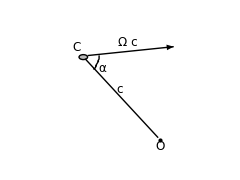

We can solve for expressions that define the constants E and L.

We know that E = T + V. We have an expression and we know that T = 1/2 mv^2, but in our case we are dealing with massless energy so T = 1/2 v^2. Using that info we get an expression for E:

E = T + V = 1/2(Ω c)^2 + 1/2 Ω^2 c^2 =Ω^2 c^2

We can also use the old cross product definition of L (L = r × v) To get an expression for that.

L = r × v = c × Ω c = Ω c^2 sin (α)

We then get the expression for V^*

V^* =  L^2/(2 r^2) + Ω^2 r^2/2  = ((Ω c^2 sin (α))^2)/(2 r^2) +Ω^2 r^2/2 = (Ω^2 c^4 sin^2(α))/(2 r^2) + (Ω^2 r^2)/2

We then use equation (7.11) to get a polynomial in terms of r. Note that this equation is simply V^* = E

V^* = E →(Ω^2 c^4 sin^2(α))/(2 r^2) + (Ω r^2)/2 = Ω^2 c^2 → c^4 sin^2(α) + r^4 = 2 c^2 r^2

r^4 - 2 c^2 r^2 + c^4 sin^2(α) = 0

The apsidal distances are the positive roots of equation  (0.4).

We let Mathematica find them for us:

```mathematica
ans = Solve[r^4 - 2 c^2 r^2 + c^4 Sin[α]^2==0, r]
```

{{r→-c √(cos(α)+1)},{r→c √(cos(α)+1)},{r→-√(c^2-c^2 cos(α))},{r→√(c^2-c^2 cos(α))}}

We can see that the positive ones are  the 2nd and 4th ones. We pull them out

```mathematica
sol1 = r/. ans[[2]]
sol2 = r/. ans[[4]]
```

c √(cos(α)+1)

√(c^2-c^2 cos(α))

To get it in the form of the book we need to use some trig idtentities.

The first solution needs the identity that cos^2(x) = 1/2(1 + cos(2 x)) → cos(2x) = 2 cos^2(x) - 1→ cos x = 2 cos^2(x/2) - 1. Applying that we get:

c √(cos(α) + 1) = c √(2 cos^2 α/2  - +1) = c √2 cos(α/2)□

The second one needs the identity sin^2(x) = 1/2(1 - cos(2x)) → cos(x) = 1 - 2 sin^2(x/2). Applying that:

√(c^2 - c^2 cos(α)) = c √(1 - cos(α)) = c √(1 - (1 - 2 sin^2(α/2))) = c √(2 sin^2(α/2)) = c √(2 sin(α/2))□

These are the major and minor axis of the ellipse. so we are done.